```mathematica
Elementary electromagnetism 2
Lihong Ao
2019271014
SZU,physics
```

```mathematica
ⅆ Subscript[B, x]=Subscript[μ, 0]/(4π)(Subscript[i, 2] Rⅆφ)/((r-R)^2+z^2)(-R Cos[φ]+r Cos[θ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])
ⅆ Subscript[B, y]=Subscript[μ, 0]/(4π)(Subscript[i, 2] Rⅆφ)/((r-R)^2+z^2)(-R Sin[φ]+r Sin[θ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])
ⅆ Subscript[B, z]=Subscript[μ, 0]/(4π)(Subscript[i, 2] Rⅆφ)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])
Subscript[B, x](θ,r,z)=Subscript[μ, 0]/(4π)∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r Subscript[i, 2] R)/((r-R)^2+z^2)(-R Cos[φ]+r Cos[θ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ
Subscript[B, y](θ,r,z)=Subscript[μ, 0]/(4π)∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r Subscript[i, 2] R)/((r-R)^2+z^2)(-R Sin[φ]+r Sin[θ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ
Subscript[B, z](θ,r,z)=Subscript[μ, 0]/(4π)∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r Subscript[i, 2] R)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ
```

```mathematica
ⅆ Subscript[B, θ]=Subscript[μ, 0]/(4π)(Subscript[i, 2] Rⅆφ)/((r-R)^2+z^2)(R Sin[θ-φ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])
ⅆ Subscript[B, r]=Subscript[μ, 0]/(4π)(Subscript[i, 2] Rⅆφ)/((r-R)^2+z^2)(r-R Cos[θ-φ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])
ⅆ Subscript[B, z]=Subscript[μ, 0]/(4π)(Subscript[i, 2] Rⅆφ)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])
Subscript[B, θ](θ,r,z)=∫_Subscript[Ω, 2] ⅆ Subscript[B, θ]=Subscript[μ, 0]/(4π)∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r Subscript[i, 2] R)/((r-R)^2+z^2)(R Sin[θ-φ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ
r^2+R^2+(h-z)^2>r^2+R^2≥2 r R
∫(a Sin[θ-φ])/(b-c Cos[θ-φ])ⅆφ=-(a Log[b-c Cos[θ-φ]])/c
Subscript[B, θ]=0

Subscript[B, r](θ,r,z)=∫_Subscript[Ω, 2] ⅆ Subscript[B, r]=Subscript[μ, 0]/(4π)∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r Subscript[i, 2] R)/((r-R)^2+z^2)(r-R Cos[θ-φ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ
≈Subscript[μ, 0]/(4π)∑_(r=Subscript[R, 3])^Subscript[R, 4] ∫_0^(2π) ∫_0^Subscript[H, 2] (r Subscript[i, 2] R)/((r-R)^2+z^2)(R Cos[θ-φ])/(r^2+ R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆφ
Subscript[B, z](θ,r,z)=∫_Subscript[Ω, 2] ⅆ Subscript[B, z]=Subscript[μ, 0]/(4π)∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r Subscript[i, 2] R)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ
```

```mathematica
Subscript[F, r]=∫_Subscript[Ω, 1] i Subscript[B, z] ⅆl=∫_Subscript[Ω, 1] i Subscript[B, z] rⅆθ=i∫_0^(2π) ∫_(x-H/2)^(x+H/2) ∫_Subscript[R, 1]^Subscript[R, 2] Subscript[B, z] rⅆrⅆzⅆθ=(Subscript[μ, 0] i Subscript[i, 2])/(4π)∫_0^(2π) ∫_(x-H/2)^(x+H/2) ∫_Subscript[R, 1]^Subscript[R, 2] ∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r^2 R)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφⅆrⅆzⅆθ
(∂Subscript[F, r])/(∂θ)|_(θ=Subscript[θ, 1])=(∂Subscript[F, r])/(∂θ)|_(θ=Subscript[θ, 2])  (∂Subscript[F, r])/(∂θ)=(∂Subscript[F, r])/(∂θ)|_(θ=0)
Subscript[F, r]=(Subscript[μ, 0] i Subscript[i, 2])/2∫_(x-H/2)^(x+H/2) ∫_Subscript[R, 1]^Subscript[R, 2] ∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r^2 R)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφⅆrⅆz
Subscript[F, z]=(Subscript[μ, 0] i i2)/2∫_(x-H/2)^(x+H/2) ∫_Subscript[R, 1]^Subscript[R, 2] ∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r^2 R)/((r-R)^2+z^2)(R Cos[θ-φ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφⅆrⅆz
```

```mathematica
i2=50;Subscript[μ, 0]=4π*10^-7;Subscript[R, 1]=.0055;Subscript[R, 2]=.011;Subscript[R, 3]=31/2000;Subscript[R, 4]=41/2000;H=.0036;Subscript[H, 2]=.007;
Subscript[μ, 0]/(4π)∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r i2 R)/((r-R)^2+z^2)(r-R Cos[θ-φ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ//Simplify
Subscript[μ, 0]/(4π)∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r i2 R)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ//Simplify
```

$Aborted

$Aborted

```mathematica
x=Table[.00001x,{x,-.03,.03}];
(Subscript[μ, 0] i i2)/(4π)∫_0^(2π) ∫_(x-H/2)^(x+H/2) ∫_Subscript[R, 1]^Subscript[R, 2] ∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r^2 R)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφⅆrⅆzⅆθ//N
(Subscript[μ, 0] i i2)/(4π)∫_0^(2π) ∫_(x-H/2)^(x+H/2) ∫_Subscript[R, 1]^Subscript[R, 2] ∫_0^(2π) ∫_Subscript[R, 3]^Subscript[R, 4] ∫_0^Subscript[H, 2] (r^2 R)/((r-R)^2+z^2)(R Cos[θ-φ])/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφⅆrⅆzⅆθ//N
```

$Aborted

$Aborted

```mathematica
i=5;Subscript[μ, 0]=4π*10^-7;R3=31/2000;R4=41/2000;Subscript[H, 2]=.007;
Subscript[B, r][r_,z_]:=Subscript[μ, 0]/(4π)∫_0^(2π) ∫_R3^R4 ∫_0^Subscript[H, 2] (r i R)/((r-R)^2+z^2)(r-R Cos[φ])/(r^2+R^2+(h-z)^2-2 r R Cos[φ])ⅆhⅆRⅆφ;
Subscript[B, z][r_,z_]:=Subscript[μ, 0]/(4π)∫_0^(2π) ∫_R3^R4 ∫_0^Subscript[H, 2] (r i R)/((r-R)^2+z^2)(z-h)/(r^2+R^2+(h-z)^2-2 r R Cos[θ-φ])ⅆhⅆRⅆφ;
VectorPlot[{Subscript[B, r][r,z],Subscript[B, z][r,z]},{r,0,.05},{z,-.03,.03}]
```

```mathematica
i=5;Subscript[μ, 0]=4π*10^-7;R3=31/2000;R4=41/2000;Subscript[H, 2]=.007;r=30/2000;z=0;
Subscript[μ, 0]/(4π)∫_0^(2π) ∫_R3^R4 ∫_0^Subscript[H, 2] (r i R)/((r-R)^2+z^2)(r-R Cos[φ])/(r^2+R^2+(h-z)^2-2 r R Cos[φ])ⅆhⅆRⅆφ//N
Clear["`*"]
```

```mathematica
i=5;
i2=50;
Subscript[μ, 0]=4π*10^-7;R1=.0055;R2=.011;R3=31/2000;R4=41/2000;H=.0036;Subscript[H, 2]=.007;n1=20;n2=1000/π;n3=10^3;n4=10;
Table[(Subscript[μ, 0] i i2)/2 1/(n1 n2 n3 n4)Total@Flatten@Table[Table[Table[Table[(i r R (ArcTan[z/(√(r^2+R^2-2 r R Cos[φ]))]+ArcTan[(-z+Subscript[H, 2])/(√(r^2+R^2-2 r R Cos[φ]))]) (r-R Cos[φ]))/(((r-R)^2+z^2) √(r^2+R^2-2 r R Cos[φ])),{r,R1,R2,1/n1}],{z,x-H/2,x+H/2,1/n4}],{φ,0,2π,1/n2}],{R,R3,R4,1/n3}],{x,-.03,.03,.0005}]
Clear["`*"]
```

{2.40595×10^-10,2.51427×10^-10,2.62826×10^-10,2.74823×10^-10,2.87453×10^-10,3.0075×10^-10,3.14753×10^-10,3.295×10^-10,3.45033×10^-10,3.61395×10^-10,3.7863×10^-10,3.96787×10^-10,4.15913×10^-10,4.3606×10^-10,4.57281×10^-10,4.79629×10^-10,5.0316×10^-10,5.2793×10^-10,5.53997×10^-10,5.81419×10^-10,6.10253×10^-10,6.40554×10^-10,6.72378×10^-10,7.05777×10^-10,7.40797×10^-10,7.7748×10^-10,8.15861×10^-10,8.55966×10^-10,8.97806×10^-10,9.41382×10^-10,9.86672×10^-10,1.03364×10^-9,1.08221×10^-9,1.13229×10^-9,1.18374×10^-9,1.23639×10^-9,1.29001×10^-9,1.34431×10^-9,1.39896×10^-9,1.45352×10^-9,1.50751×10^-9,1.56032×10^-9,1.61129×10^-9,1.65963×10^-9,1.70445×10^-9,1.74476×10^-9,1.77949×10^-9,1.80745×10^-9,1.82742×10^-9,1.83809×10^-9,1.83821×10^-9,1.82654×10^-9,1.80196×10^-9,1.76356×10^-9,1.7107×10^-9,1.6431×10^-9,1.56096×10^-9,1.46501×10^-9,1.3566×10^-9,1.23769×10^-9,1.11088×10^-9,9.79319×10^-10,8.46583×10^-10,7.16517×10^-10,5.93026×10^-10,4.79846×10^-10,3.80318×10^-10,2.97195×10^-10,2.32484×10^-10,1.87356×10^-10,1.62117×10^-10,1.56245×10^-10,1.68478×10^-10,1.9694×10^-10,2.39303×10^-10,2.92941×10^-10,3.55091×10^-10,4.22999×10^-10,4.94036×10^-10,5.65795×10^-10,6.36158×10^-10,7.03335×10^-10,7.65888×10^-10,8.22718×10^-10,8.73054×10^-10,9.16424×10^-10,9.52614×10^-10,9.81627×10^-10,1.00365×10^-9,1.019×10^-9,1.0281×10^-9,1.03144×10^-9,1.02957×10^-9,1.02303×10^-9,1.01239×10^-9,9.98176×10^-10,9.80918×10^-10,9.61099×10^-10,9.39171×10^-10,9.15548×10^-10,8.90603×10^-10,8.64668×10^-10,8.3804×10^-10,8.10979×10^-10,7.83709×10^-10,7.56425×10^-10,7.29293×10^-10,7.02451×10^-10,6.76017×10^-10,6.50085×10^-10,6.24732×10^-10,6.00021×10^-10,5.75998×10^-10,5.52697×10^-10,5.30143×10^-10,5.08351×10^-10,4.8733×10^-10,4.67081×10^-10,4.47599×10^-10,4.28876×10^-10,4.109×10^-10}

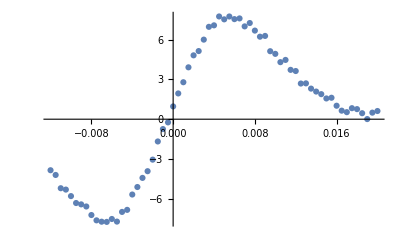

```mathematica
tab1={-3.852381151991537,-4.2087317661994916,-5.2102561939331977,-5.3126610808673007,-5.8044421969763675,-6.3268029466186029,-6.4285676601577393,-6.5876508814358505,-7.2332473917166737,-7.6348559891149,-7.7367841138745774,-7.7515926853533159,-7.5319098532420412,-7.7284657165681381,-6.998285824812271,-6.8427717734402336,-5.685556675872192,-5.1191100696490253,-4.4302916037523161,-3.924466789193815,-3.0520736140016709,-1.6807245024360782,-0.74529438664862369,-0.23880057395879106,0.96416778417443538,1.9443483534131918,2.7907072965627844,3.9157266878929704,4.8207674523948612,5.1429233400139651,6.00602708254587,6.971999130648058,7.0844538310867051,7.7548674976786316,7.53679337674734,7.7528419418008809,7.5534451045331821,7.607095579142622,7.0057159911658005,7.2596159686112571,6.6878997053491958,6.22738831143387,6.2854558758722305,5.13159832756827,4.93216904634405,4.3054930396434656,4.4739315132582629,3.7245321075449453,3.6364802079935714,2.6916242705012081,2.7051204891598957,2.3082623218447722,2.0863211084670894,1.8906173089336917,1.566485134230561,1.619476405129312,1.0169637381323184,0.64466511227362844,0.53184915315546277,0.83222426708181274,0.76070142978059607,0.45259320592571051,0.0094062923132014475,0.49513460361488626,0.61796390545813651};
ListPlot[Transpose@{Table[x,{x,-.012,.02,.0005}],tab1},PlotRange->All]
```

```mathematica
ListPlot[Transpose@{Table[x,{x,-.02,.03,.0005}],{-0.026947508958818367,-0.028440835292355748,-0.029973754753228388,-0.031567104335279428,-0.0333776400349266,-0.035199953489655655,-0.037257899238829495,-0.039490800625953781,-0.042089297640638623,-0.044731749399585685,-0.04768235027303902,-0.050747032846382933,-0.054464986475241339,-0.057791230620116707,-0.061975802127980373,-0.066872714703682945,-0.07135295762743965,-0.077199393774868064,-0.084083062565573963,-0.0923545133994077,-0.10640487792902809,,-0.13354088477402692,-0.14929332845347787,-0.15887751818233653,-0.17325836469167122,-0.18624376794230013,,-0.18182605112290773,-0.15464223423816748,-0.14204057042458373,-0.12349496418394801,-0.12168794745652178,-0.10885016774870682,-0.096507354461337513,-0.084841779699516451,-0.084710838198237326,-0.058749916036029859,-0.0566666302307004,-0.00700994438723157,-0.016975284203066821,0.026162601977042232,0.04481532516970077,0.050684000354301872,0.077741958790234378,0.093901444081840424,,0.094383790052797067,0.1231903396830063,0.11963961994484862,0.12934131821980621,,0.16544001417011112,0.20168635938292923,0.19012318656545713,0.1795701690907332,0.164342201216119750,14350416730088789,0.13231148366085588,0.12097491170957553,0.10256138769206657,0.092158811606485536,0.083881038367047966,0.078114889285929356,0.071245305782295709,0.0668946188353301,0.062411382559933948,0.057797640323319577,0.054348855511503036,0.05067118241116652,,0.044807362513609728,0.042045294829010871,0.039695370136044517,0.037300049462947849,0.035180300897838856,0.033350112384936459,0.03156392694093646,0.029971806709900628,0.028419962456587289,0.027007664625729788,0.025626494201330757,0.024296422573042875,0.023145766827812914,0.02197234258966071,,0.0199645755795832,0.018980406169934572,0.01812047457116428,0.017345353419212728,0.016571260753545244,,0.015095324022728063,0.014443519247892445,0.013835483724746744,,0.012646977032972129,0.0120962300802607,0.011585161503310182,0.01112185090568038,0.01066618320523044}}]
```

-Graphics-

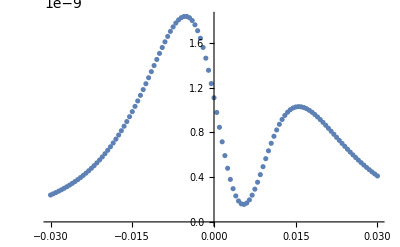

```mathematica
ListPlot[Transpose@{Table[x,{x,-.03,.03,.0005}],{2.405950772202768*^-10,2.5142702836596755*^-10,2.628256673464403*^-10,2.7482296568834906*^-10,2.8745262928495107*^-10,3.0075015894622805*^-10,3.1475290538572977*^-10,3.2950011659622785*^-10,3.4503297514828413*^-10,3.6139462245553087*^-10,3.7863016647679473*^-10,3.967866686557508*^-10,4.159131051197533*^-10,4.3606029625558796*^-10,4.5728079773453443*^-10,4.796287448544597*^-10,5.031596406839563*^-10,5.279300769136233*^-10,5.539973745236718*^-10,5.81419129347846*^-10,6.102526453371057*^-10,6.405542357940422*^-10,6.723783700608373*^-10,7.057766401130839*^-10,7.407965182714417*^-10,7.774798738522944*^-10,8.158612131338536*^-10,8.559656036625958*^-10,8.978062408810773*^-10,9.413816126255948*^-10,9.866722156400836*^-10,1.033636778448563*^-9,1.0822079474769797*^-9,1.1322873992031556*^-9,1.1837403516092925*^-9,1.2363894649173894*^-9,1.2900081464878852*^-9,1.3443133102554377*^-9,1.3989576899822278*^-9,1.4535218711156855*^-9,1.5075062915542349*^-9,1.5603235704933111*^-9,1.6112916595082141*^-9,1.65962847249716*^-9,1.7044488397946066*^-9,1.7447648410312423*^-9,1.7794907888146637*^-9,1.8074543391024938*^-9,1.8274153595397334*^-9,1.8380942436720618*^-9,1.8382112492985514*^-9,1.8265380802993175*^-9,1.801962232016201*^-9,1.7635634975724736*^-9,1.7107004381947482*^-9,1.6431025793798374*^-9,1.5609617486720772*^-9,1.465013617892897*^-9,1.3565986194320879*^-9,1.2376905688052122*^-9,1.110882158910294*^-9,9.793194461118964*^-10,8.465825938847515*^-10,7.165169895341233*^-10,5.930263257274859*^-10,4.798458483342443*^-10,3.8031818527073137*^-10,2.971948881152345*^-10,2.324837459834533*^-10,1.8735570124890051*^-10,1.6211716855302051*^-10,1.562453899455986*^-10,1.6847762537553727*^-10,1.9694042202359227*^-10,2.393032169879219*^-10,2.929408350832757*^-10,3.5509143762798144*^-10,4.229994488590773*^-10,4.940363008140242*^-10,5.657950280764106*^-10,6.361575223461521*^-10,7.03335481319304*^-10,7.65887715296066*^-10,8.227175282663957*^-10,8.730544244008569*^-10,9.164244852037818*^-10,9.526135111444573*^-10,9.816265257988958*^-10,1.0036466006183066*^-9,1.0189952645194515*^-9,1.0280960874318147*^-9,1.03144242239151*^-9,1.029569786903145*^-9,1.0230329724905415*^-9,1.0123876887404292*^-9,9.98176362526389*^-10,9.8091760750215*^-10,9.610988350935705*^-10,9.391714788718776*^-10,9.155483345120939*^-10,8.906025655967631*^-10,8.646679822931187*^-10,8.380402589888073*^-10,8.109788140453173*^-10,7.837091273225376*^-10,7.564253176815733*^-10,7.292928427905838*^-10,7.024512173152793*^-10,6.760166733955043*^-10,6.500847098039937*^-10,6.247324940425956*^-10,6.00021095550443*^-10,5.759975388348336*^-10,5.526966732836567*^-10,5.301428621996765*^-10,5.083514976584697*^-10,4.873303505083033*^-10,4.67080766511427*^-10,4.4759872052427697*^-10,4.2887574093143124*^-10,4.108997164455069*^-10}}]
```

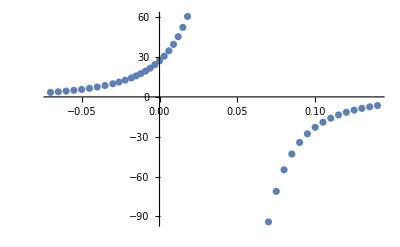

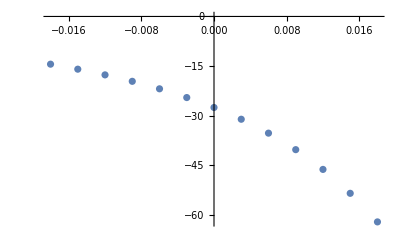

```mathematica
Subscript[tab2, i+5]={3.4158,3.85708,4.36897,4.96466,5.65706,6.46648,7.42048,8.54671,9.90329,11.1602,12.6363,14.347450167733189,15.83917155720864,17.518607840260472,19.444928282446654,21.663627847524452,24.242088707851792,27.17556776286661,30.651806837243456,34.733781385475474,39.578089372974787,45.375622957542667,52.386431096583728,60.622433670309192,-94.203467261997545,-71.166036634189084,-54.9381674006266,-43.058596929855739,-34.355081129686525,-27.8348336889661,-22.907476810391085,-19.06355839988127,-16.035373402909766,-13.587627784037421,-11.608019174685921,-9.97130525879221,-8.6134316233727581,-7.4791118248334811,-6.5060864630947384,-5.693519822306035,-4.9927210780589037,-4.3962868328274887,-3.8753029783753612,-3.4379517086827218,-3.0481902237512184,-2.7183063215963719,-2.4218257276923976};
ListPlot[Transpose@{Flatten@{Table[x,{x,-0.07,-0.03,0.005}],-0.026,-0.022,Table[x,{x,-.018,.018,.003}],Table[x,{x,0.07,0.18,0.005}]},Subscript[tab2, i+5]},PlotRange->All]
Subscript[tab2, i-5]={-14.431876101079817,-15.947804131988505,-17.670486112336416,-19.619021060039444,-21.885742705793646,-24.530497117275253,-27.534326655996864,-31.090964216779135,-35.296653226393651,-40.28978673621328,-46.267266240104981,-53.49703517517343,-62.143031004815867};
ListPlot[Transpose@{Table[x,{x,-.018,.018,.003}],Subscript[tab2, i-5]},PlotRange->All]
```

```mathematica
(δ ω̄(Γ))/δΓ=0,(δ^2 ω̄(Γ))/δΓ^2<0
(δ Subscript[ω, c](Γ))/δΓ=0,(δ^2 Subscript[ω, c](Γ))/δΓ^2<0
ω̄=1/T∫_0^T ωⅆt
```

```mathematica
η=Subscript[p, eff]/p=(ϵi-i^2 R-Subscript[p, other])/ϵi=1-(i R)/ϵ-Subscript[p, other]/ϵi
i^2 R>Subscript[p, other]->ⅆη/ⅆi<0
ⅆi/ⅆω<0->ⅆη/ⅆω>0
```

```mathematica
z|_(Γ(r,θ))=z|_(Γ(r,θ+π))     β=ⅆω/ⅆt          Subscript[M, L]^(->)     B^(->) Subscript[e, θ]^(->)=0
M^(->)=∫_Γ r i^(->)* B^(->)ⅆl=i∫_Γ r B Sin φⅆl Subscript[e, M]^(->)=(A β^2+Subscript[M, L])Subscript[e, M]^(->)     (ϵ/R∫_Γ r B Sin φⅆl>Subscript[M, L])
i=Subscript[ϵ, eff]/R=1/R(ϵ-∫_Γ|v^(->) *B^(->) |ⅆl-L ⅆi/ⅆt)=1/R(ϵ-∫_Γ|r ω^(->)*B^(->) |ⅆl-L ⅆi/ⅆt)=1/R(ϵ-ω∫_Γ r B Sin φⅆl-L ⅆi/ⅆt)
ξ=∫_Γ r B Sin φⅆl
i(t)=ⅇ^(-(R t)/L) (Subscript[i, 0]+(ⅇ^((R ψ)/L) (ϵ-ξ ω[ψ]))/Lψ0t)≈Subscript[i, 0]+((-ⅇ^(-(R t)/L)+1) (ϵ-ξ ω))/R            Subscript[i, c]=(ϵ-ω ξ)/R         
A β+Subscript[M, L]=∫_Γ i r B Sin φⅆl=i∫_Γ r B Sin φⅆl=k/R(ϵ-ω ξ)ξ
A Δω+∫_0^T Subscript[M, L] ⅆt=∫_0^T Subscript[M, L] ⅆt=∫_0^T ∫_Γ i r B Sin φⅆlⅆt  =^modelling∫_0^T k Subscript[i, c]∫_Γ r B Sin φⅆlⅆt =k/R∫_0^Subscript[t, 0] (ϵ-ω ξ)ξⅆt       (Δω=∫_0^T βⅆt)
Subscript[ΔE, k]+∫_0^(2π) Subscript[M, L] ⅆθ=∫_0^(2π) Subscript[M, L] ⅆθ=k/R∫_0^Subscript[θ, 0] (ϵ-ω ξ)ξⅆθ       (Subscript[ΔE, k]=∫_0^(2π) Subscript[M, L] ⅆθ)
2π OverBar[Subscript[M, L]]=k/R∫_0^Subscript[θ, 0] (ϵ-ω ξ)ξⅆθ =k/R(ϵ∫_0^Subscript[θ, 0] ξⅆθ-∫_0^Subscript[θ, 0] ω ξ^2 ⅆθ)
∫_0^Subscript[θ, 0] ω ξ^2 ⅆθ=Subscript[(∫ωⅆθ ξ^2), 0]^Subscript[θ, 0]-2∫_0^Subscript[θ, 0] ∫ωⅆθ ξ ⅆξ/ⅆθ ⅆθ=∫_0^Subscript[θ, 0] ωⅆθ(Subscript[ξ, θ=Subscript[θ, 0]]^2-Subscript[ξ, θ=0]^2)-2∫_Subscript[ξ, θ=0]^Subscript[ξ, θ=Subscript[θ, 0]] ξ∫ωⅆθⅆξ
∫_Subscript[ξ, θ=0]^Subscript[ξ, θ=Subscript[θ, 0]] ξ∫ωⅆθⅆξ=E(∫ωⅆθ(ξ))≈0
Subscript[ω, c]=1/T∫_0^T ωⅆt≈1/(2π)∫_0^(2π) ωⅆθ≈1/Subscript[θ, 0]∫_0^Subscript[θ, 0] ωⅆθ
∫_0^Subscript[θ, 0] ω ξ^2 ⅆθ≈Subscript[θ, 0] Subscript[ω, c](Subscript[ξ, θ=Subscript[θ, 0]]^2-Subscript[ξ, θ=0]^2)
Subscript[ω, c]=1/(Subscript[ξ, θ=Subscript[θ, 0]]^2-Subscript[ξ, θ=0]^2)(ϵ/Subscript[θ, 0]∫_0^Subscript[θ, 0] ξⅆθ-(2π R OverBar[Subscript[M, L]])/(Subscript[θ, 0] k))=^(Subscript[ξ, θ=Subscript[θ, 0]]=-Subscript[ξ, θ=0]=Subscript[ξ, m]/2)1/Subscript[ξ, m]^2(ϵ/Subscript[θ, 0]∫_0^Subscript[θ, 0] ξⅆθ-(2π R OverBar[Subscript[M, L]])/(Subscript[θ, 0] k))
(ϵ k)/(2π R)∫_0^Subscript[θ, 0] ξⅆθ>OverBar[Subscript[M, L]]
(*1/R(Subscript[((ϵ-ω ξ)∫ξⅆθ), 0]^Subscript[θ, 0]-∫_0^Subscript[θ, 0] (ⅆ(ϵ-ω ξ))/ⅆθ∫ξⅆθⅆθ)
Subscript[((ϵ-ω ξ)∫ξⅆθ), 0]^Subscript[θ, 0]=(ϵ-ω(Subscript[θ, 0]) ξ(Subscript[θ, 0]))∫_0^Subscript[θ, 0] ξⅆθ
∫_0^Subscript[θ, 0] (ⅆ(ϵ-ω ξ))/ⅆθ∫ξⅆθⅆθ=Subscript[((ϵ-ω ξ)∫ξⅆθ), 0]^Subscript[θ, 0]-∫_0^Subscript[θ, 0] (ϵ-ω ξ)ξⅆθ=(ϵ-ω(Subscript[θ, 0]) ξ(Subscript[θ, 0]))∫_0^Subscript[θ, 0] ξⅆθ-∫_0^Subscript[θ, 0] ϵξⅆθ+∫_0^Subscript[θ, 0] ω ξ^2 ⅆθ
∫_0^Subscript[θ, 0] ϵξⅆθ=∫_0^Subscript[ξ, 0] ϵξ ⅆθ/ⅆξ ⅆξ,∫_0^Subscript[θ, 0] ω ξ^2 ⅆθ=∫_0^Subscript[ξ, 0] ω ξ^2 ⅆθ/ⅆξ ⅆξ
2π OverBar[Subscript[M, L]]=1/R(-ϵ∫_0^Subscript[ξ, 0] ξ ⅆθ/ⅆξ ⅆξ+∫_0^Subscript[ξ, 0] ω ξ^2 ⅆθ/ⅆξ ⅆξ)*)

ξ=const->Subscript[ω, c]=ϵ/ξ-(Subscript[M, L] R)/ξ^2         
(ⅆ Subscript[ω, c])/ⅆξ>0 ( (Subscript[M, L] R)/ϵ<ξ<(2 Subscript[M, L] R)/ϵ),Subscript[ω, c max]=Subscript[ϵ, 0]^2/(4 Subscript[M, L] R),Subscript[ξ, best]=(2 Subscript[M, L] R)/ϵ
ξ(Γ)=(2 Subscript[M, L] R)/ϵ,(Subscript[ξ, max]>(2 Subscript[M, L] R)/ϵ)             (δξ(Γ))/δΓ=0,(δ^2 ξ(Γ))/δΓ^2<0,(Subscript[ξ, max]<(2 Subscript[M, L] R)/ϵ)
Γ∈rOz Γ∈𝔼^3
∫_Γ r B^(->)ⅆl=∫_Γ r B Cos φⅆl
ξ=∫_Γ r B Sin φⅆl=∫_Γ r (Subscript[e, θ]^(->)*B^(->)) ⅆl=∫_S rot(r Subscript[e, θ]^(->)*B^(->))ⅆS
rot(r Subscript[e, θ]^(->)*B^(->))=Subscript[e, θ]^(->)div(r B^(->))-r B^(->) div Subscript[e, θ]^(->)=Subscript[e, θ]^(->)div(r B^(->))
ξ=∫_S div(r B^(->))ⅆS
```

```mathematica
H^(->)=-div Subscript[V, m],div B^(->)=0
B^(->)n^(->)=0
B^(->)=Subscript[μ, 0] Subscript[μ, r] H^(->)   B^(->)=Subscript[μ, 0](H^(->)+M^(->))      M^(->)=M Subscript[e, z]^(->),M=880(A/m)
```

```mathematica
(r,θ,z)    (φ,ζ)
Subscript[μ, 0]/(4π)∫(i ⅆl)/Δr^2 n^(->)=Subscript[μ, 0]/(4π)∫_Subscript[z, 1]^Subscript[z, 2] ∫_0^(2π) (i R √((r Cos[θ-φ]-R)^2+(z-ζ)^2))/(((z-ζ)^2+r^2+R^2+2 r R Cos[θ-φ])^(3/2))ⅆφⅆζ
```

```mathematica
(r,z)   Z
Subscript[B, z]=Subscript[μ, 0]/(4π)∫(i ⅆl)/Δr^2 n^(->)=Subscript[μ, 0]/(4π)∫_Subscript[Z, 0]^(Subscript[Z, 0]+h) ((i (r-R))/(((Z-z)^2+(r-R)^2)^(3/2))-(i (r+R))/(((Z-z)^2+(r+R)^2)^(3/2)))ⅆZ=(i Subscript[μ, 0])/(4π)(1/(r-R)((z-Subscript[Z, 0])/(√((r-R)^2+(z-Subscript[Z, 0])^2))+(h-z+Subscript[Z, 0])/(√((r-R)^2+(h-z+Subscript[Z, 0])^2)))-1/(r+R)((z-Subscript[Z, 0])/(√((r+R)^2+(z-Subscript[Z, 0])^2))+(h-z+Subscript[Z, 0])/(√((r+R)^2+(h-z+Subscript[Z, 0])^2))))(->)^(Subscript[Z, 0]=0)(i Subscript[μ, 0])/(4π)(1/(r-R)(z/(√((r-R)^2+z^2))+(h-z)/(√((r-R)^2+(h-z)^2)))-1/(r+R)(z/(√((r+R)^2+z^2))+(h-z)/(√((r+R)^2+(h-z)^2))))
Subscript[B, r]=Subscript[μ, 0]/(4π)∫_Subscript[Z, 0]^(Subscript[Z, 0]+h) ((i (z-Z))/(((Z-z)^2+(r-R)^2)^(3/2))-(i(z-Z))/(((Z-z)^2+(r+R)^2)^(3/2)))ⅆZ=(i Subscript[μ, 0])/(4π)(1/(√((r-R)^2+(z-Subscript[Z, 0])^2))-1/(√((r+R)^2+(z-Subscript[Z, 0])^2))-1/(√((r-R)^2+(h-z+Subscript[Z, 0])^2))+1/(√((r+R)^2+(h-z+Subscript[Z, 0])^2)))(->)^(Subscript[Z, 0]=0)(i Subscript[μ, 0])/(4π)(1/(√((r-R)^2+z^2))-1/(√((r+R)^2+z^2))-1/(√((r-R)^2+(h-z)^2))+1/(√((r+R)^2+(h-z)^2)))
```

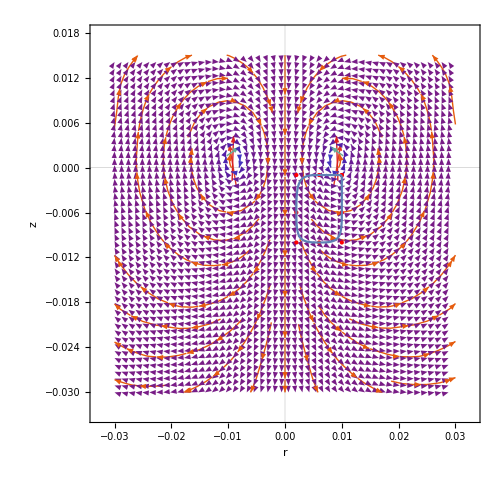

```mathematica
R=0.009;i=1;h=0.002;Subscript[μ, 0]=1;points={{0.01,-0.001},{0.006,-0.001},{0.002,-0.001},{0.002,-0.006},{0.002,-0.01},{0.006,-0.01},{0.01,-0.01},{0.01,-0.006},{0.01,-0.001}};Γ=BSplineFunction[points,SplineClosed->True];
Show[VectorPlot[{(i Subscript[μ, 0])/(4π)(1/(√((r-R)^2+z^2))-1/(√((r+R)^2+z^2))-1/(√((r-R)^2+(h-z)^2))+1/(√((r+R)^2+(h-z)^2))),(i Subscript[μ, 0])/(4π)(1/(r-R)(z/(√((r-R)^2+z^2))+(h-z)/(√((r-R)^2+(h-z)^2)))-1/(r+R)(z/(√((r+R)^2+z^2))+(h-z)/(√((r+R)^2+(h-z)^2))))},{r,-.03,.03},{z,-.03,.015},VectorPoints->50,VectorColorFunction->"Rainbow",AxesLabel->{r,z},VectorScale->{.08,.2},ImageSize->500,StreamPoints->Coarse,PlotTheme->"Scientific",AxesLabel->{"r/m","z/m"}],Graphics[{Green,Red,Point[points]}],ParametricPlot[Γ[t],{t,0,1}]]
```

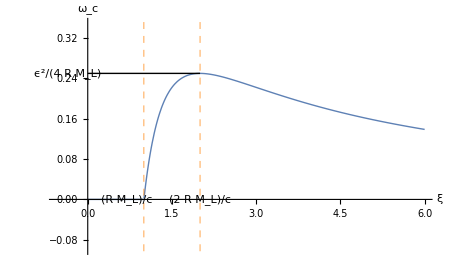

```mathematica
Plot[Piecewise[{{-999,ξ<0},{0,0<ξ<1},{1/ξ-1/ξ^2,ξ≥1}}],{ξ,-.55,6},PlotStyle->Thick,PlotRange->{-.1,.35},ImageSize->450,GridLines->{{1,2},{}},GridLinesStyle->Directive[Orange,Dashed],Ticks->None,AxesLabel->{ξ,Subscript[ω, c]},Epilog->{Text[(Subscript[M, L] R)/ϵ,{.7,0}],Text[(2 Subscript[M, L] R)/ϵ,{2,0}],Text[ϵ^2/(4 Subscript[M, L] R),{-.35,1/4}],Line[{{0,1/4},{2,1/4}}]}]
```

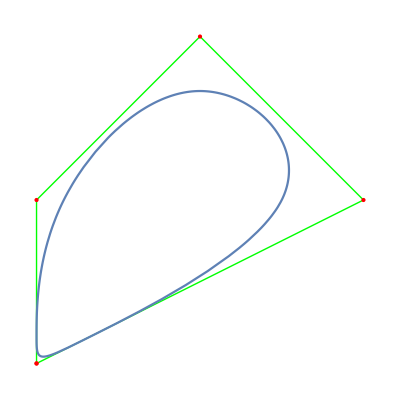

```mathematica
Γ=BSplineFunction[{{0,0},{0,1},{1,2},{2,1},{0,0}},SplineClosed->True];
Show[Graphics[{Green,Line[{{0,0},{0,1},{1,2},{2,1},{0,0}}],Red,Point[{{0,0},{0,1},{1,2},{2,1},{0,0}}]}],ParametricPlot[Γ[t],{t,0,1}]]
```

```mathematica
Unconvergence occors on substeps999999(∨⏜∨)
```

```mathematica
ρ    N     d
```